```mathematica
f1[r_,θ_]:=(A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)Exp[-(A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)^2 /(2 (σ^2+σs^2))];
f1[r,θ]
series1=Series[f1[r,θ],{r,0,2}];(*obtain the Taylor series up to 3th order*)
```

ⅇ^(-((-μs+A (α0+r Cos[θ])^2+B r Sin[θ])^2)/(2 (σ^2+σs^2))) (-μs+A (α0+r Cos[θ])^2+B r Sin[θ])

```mathematica
eq1[μs_,σs_]:=Integrate[ series1,{r,0,ro},{θ,0,2 Pi}]
eq1[μs,σs]
```

1/(6 (σ^2+σs^2)^2)ⅇ^(-((-A α0^2+μs)^2)/(2 (σ^2+σs^2))) π ro (4 A^5 ro^2 α0^8-12 A^4 ro^2 α0^6 μs+A^3 ro^2 α0^4 (B^2 α0^2+12 μs^2-14 (σ^2+σs^2))+A^2 ro^2 α0^2 μs (-3 B^2 α0^2-4 μs^2+16 (σ^2+σs^2))-μs (12 (σ^2+σs^2)^2+B^2 ro^2 (μs^2-3 (σ^2+σs^2)))+A (3 B^2 ro^2 α0^2 (μs^2-σ^2-σs^2)+2 (σ^2+σs^2) (6 α0^2 (σ^2+σs^2)+ro^2 (-μs^2+σ^2+σs^2))))

```mathematica
f2[r_,θ_]:=((A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)^2-(σs^4-σ^4)/(2 σs^2))Exp[-(A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)^2 /(2 (σ^2+σs^2))];f2[r,θ]
series2=Series[f2[r,θ],{r,0,2}];
```

ⅇ^(-((-μs+A (α0+r Cos[θ])^2+B r Sin[θ])^2)/(2 (σ^2+σs^2))) (-(-σ^4+σs^4)/(2 σs^2)+(-μs+A (α0+r Cos[θ])^2+B r Sin[θ])^2)

```mathematica
eq2[μs_,σs_]:=Integrate[ series2,{r,0,ro},{θ,0,2 Pi}]
eq2[μs,σs]
```

1/(12 σs^2 (σ^2+σs^2)^2)ⅇ^(-((-A α0^2+μs)^2)/(2 (σ^2+σs^2))) π ro (8 A^6 ro^2 α0^10 σs^2-32 A^5 ro^2 α0^8 μs σs^2+12 (σ^2+σs^2)^2 (σ^4+2 μs^2 σs^2-σs^4)-4 A^3 ro^2 α0^4 μs (2 σ^4-23 σ^2 σs^2+σs^2 (2 B^2 α0^2+8 μs^2-25 σs^2))+B^2 ro^2 (2 μs^4 σs^2-(σ^2-5 σs^2) (σ^2+σs^2)^2+μs^2 (σ^4-10 σ^2 σs^2-11 σs^4))+2 A^4 ro^2 α0^6 (2 σ^4-22 σ^2 σs^2+σs^2 (B^2 α0^2+24 (μs^2-σs^2)))+A^2 α0^2 (24 α0^2 σs^2 (σ^2+σs^2)^2+B^2 ro^2 α0^2 (σ^4+12 μs^2 σs^2-10 σ^2 σs^2-11 σs^4)+2 ro^2 (4 μs^4 σs^2-3 (σ^2-5 σs^2) (σ^2+σs^2)^2+2 μs^2 (σ^4-13 σ^2 σs^2-14 σs^4)))-2 A μs (B^2 ro^2 α0^2 (σ^4+4 μs^2 σs^2-10 σ^2 σs^2-11 σs^4)-(σ^2+σs^2) (-24 α0^2 σs^2 (σ^2+σs^2)+ro^2 (σ^4+2 μs^2 σs^2-4 σ^2 σs^2-5 σs^4))))

```mathematica
sol=Solve[{eq1[μs,σs]==0,eq2[μs,σs]==0,σs>0,μs>0}/.{A->915,B->0.9,ro->0.0046,σ->0.042,α0->0},{μs,σs},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μs→0.00322131,σs→0.0419105}}

```mathematica
sol=Solve[{eq1[μs,σs]==0,eq2[μs,σs]==0,σs>0,μs>0}/.{A->915,B->0.9,ro->0.0046,σ->0.042,α0->0.01},{μs,σs},Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μs→0.0963445,σs→0.0591578}}

```mathematica
(*将代码集合在一起*)
degree=4;
(*n=5,6 时不能给出数值解    n=4是最高阶的数值解*) 
f1[r_,θ_]:=(A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)Exp[-(A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)^2 /(2 (σ^2+σs^2))]
f1[r,θ]
series1=Series[f1[r,θ],{r,0,degree}];
eq1[μs_,σs_]:=Integrate[ series1,{r,0,ro},{θ,0,2 Pi}];

f2[r_,θ_]:=((A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)^2-(σs^4-σ^4)/(2 σs^2))Exp[-(A (r Cos[θ]+α0)^2+B r Sin[θ]-μs)^2 /(2 (σ^2+σs^2))]
f2[r,θ]
series2=Series[f2[r,θ],{r,0,degree}];
eq2[μs_,σs_]:=Integrate[ series2,{r,0,ro},{θ,0,2 Pi}];
```

ⅇ^(-((-μs+A (α0+r Cos[θ])^2+B r Sin[θ])^2)/(2 (σ^2+σs^2))) (-μs+A (α0+r Cos[θ])^2+B r Sin[θ])

ⅇ^(-((-μs+A (α0+r Cos[θ])^2+B r Sin[θ])^2)/(2 (σ^2+σs^2))) (-(-σ^4+σs^4)/(2 σs^2)+(-μs+A (α0+r Cos[θ])^2+B r Sin[θ])^2)

```mathematica
sol=NSolve[{eq1[μs,σs]==0,eq2[μs,σs]==0,σs>0,μs>0}/.{A->915.52,B->0.9246,ro->0.00465,σ->0.04247,α0->0.},{μs,σs},Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μs→0.00329359,σs→0.0423786}}

```mathematica
sol=NSolve[{eq1[μs,σs]==0,eq2[μs,σs]==0,σs>0,μs>0}/.{A->915.52,B->0.9246,ro->0.00465,σ->0.04247,α0->Pi/360},{μs,σs},Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μs→0.0704995,σs→0.0523014}}

```mathematica
0.0704995379864147-0.003330111078964148 <  915.52*(Pi/360)^2
915.52*(Pi/360)^2
(*使用A 拟合得到的曲线，平移后比原始二次项的曲线低一些，因而与论文中结论*)
```

True

0.0697208

```mathematica
LaunchKernels[];
(*launch all available kernels*)
AbsoluteTiming[sol=ParallelTable[Quiet[NSolve[{eq1[μs,σs]==0,eq2[μs,σs]==0,0<σs<1,0<μs<1}/.{A->915.52,B->0.9246,ro->0.00465,σ->0.04247,α0->i*Pi/(60*180)},{μs,σs},Reals]]//Select[RegionMember[ImplicitRegion[0<μs<1&&0<σs<1,{μs,σs}],{#[[1,2]],#[[2,2]]}]&],{i,-30,30}]];

sol
muVals=sol[[All,1,1,2]];
α0=i*Pi/(60*180);
alpha0=Table[N[α0]/.i->n,{n,-30,30}];
Export[{NotebookDirectory[]<>"myfile_degree4.csv"},{alpha0,muVals},"CSV"]
```

LaunchKernels::nodef: Some subkernels are already running. Not launching default kernels again.

{{{μs→0.0704995,σs→0.0523014}},{{μs→0.0661145,σs→0.0518126}},{{μs→0.0618761,σs→0.0513193}},{{μs→0.0577845,σs→0.050824}},{{μs→0.05384,σs→0.0503293}},{{μs→0.0500426,σs→0.0498373}},{{μs→0.0463926,σs→0.0493503}},{{μs→0.04289,σs→0.0488704}},{{μs→0.0395351,σs→0.0483993}},{{μs→0.0363278,σs→0.0479389}},{{μs→0.0332683,σs→0.0474909}},{{μs→0.0303568,σs→0.0470567}},{{μs→0.0275934,σs→0.0466379}},{{μs→0.0249781,σs→0.0462357}},{{μs→0.0225112,σs→0.0458513}},{{μs→0.0201927,σs→0.0454858}},{{μs→0.0180229,σs→0.0451402}},{{μs→0.0160019,σs→0.0448154}},{{μs→0.0141298,σs→0.0445121}},{{μs→0.0124067,σs→0.044231}},{{μs→0.0108329,σs→0.0439727}},{{μs→0.00940849,σs→0.0437376}},{{μs→0.00813358,σs→0.0435264}},{{μs→0.00700831,σs→0.0433392}},{{μs→0.00603281,σs→0.0431765}},{{μs→0.0052072,σs→0.0430384}},{{μs→0.00453156,σs→0.0429251}},{{μs→0.00400597,σs→0.0428369}},{{μs→0.00363051,σs→0.0427738}},{{μs→0.00340521,σs→0.0427359}},{{μs→0.00333011,σs→0.0427233}},{{μs→0.00340521,σs→0.0427359}},{{μs→0.00363051,σs→0.0427738}},{{μs→0.00400597,σs→0.0428369}},{{μs→0.00453156,σs→0.0429251}},{{μs→0.0052072,σs→0.0430384}},{{μs→0.00603281,σs→0.0431765}},{{μs→0.00700831,σs→0.0433392}},{{μs→0.00813358,σs→0.0435264}},{{μs→0.00940849,σs→0.0437376}},{{μs→0.0108329,σs→0.0439727}},{{μs→0.0124067,σs→0.044231}},{{μs→0.0141298,σs→0.0445121}},{{μs→0.0160019,σs→0.0448154}},{{μs→0.0180229,σs→0.0451402}},{{μs→0.0201927,σs→0.0454858}},{{μs→0.0225112,σs→0.0458513}},{{μs→0.0249781,σs→0.0462357}},{{μs→0.0275934,σs→0.0466379}},{{μs→0.0303568,σs→0.0470567}},{{μs→0.0332683,σs→0.0474909}},{{μs→0.0363278,σs→0.0479389}},{{μs→0.0395351,σs→0.0483993}},{{μs→0.04289,σs→0.0488704}},{{μs→0.0463926,σs→0.0493503}},{{μs→0.0500426,σs→0.0498373}},{{μs→0.05384,σs→0.0503293}},{{μs→0.0577845,σs→0.050824}},{{μs→0.0618761,σs→0.0513193}},{{μs→0.0661145,σs→0.0518126}},{{μs→0.0704995,σs→0.0523014}}}

{C:\Jupyter_Python\EVE-spectrum-correction\mma_proof\myfile_degree4.csv}

{-0.00872665,-0.00843576,-0.00814487,-0.00785398,-0.00756309,-0.00727221,-0.00698132,-0.00669043,-0.00639954,-0.00610865,-0.00581776,-0.00552688,-0.00523599,-0.0049451,-0.00465421,-0.00436332,-0.00407243,-0.00378155,-0.00349066,-0.00319977,-0.00290888,-0.00261799,-0.00232711,-0.00203622,-0.00174533,-0.00145444,-0.00116355,-0.000872665,-0.000581776,-0.000290888,0.,0.000290888,0.000581776,0.000872665,0.00116355,0.00145444,0.00174533,0.00203622,0.00232711,0.00261799,0.00290888,0.00319977,0.00349066,0.00378155,0.00407243,0.00436332,0.00465421,0.0049451,0.00523599,0.00552688,0.00581776,0.00610865,0.00639954,0.00669043,0.00698132,0.00727221,0.00756309,0.00785398,0.00814487,0.00843576,0.00872665}

```mathematica
Export[{NotebookDirectory[]<>"myfile_degree2.csv"},{alpha0,muVals},"CSV"]
```

{C:\Jupyter_Python\EVE-spectrum-correction\mma_proof\myfile_degree2.csv}

```mathematica
α0
```

{-π/360,-(29 π)/10800,-(7 π)/2700,-π/400,-(13 π)/5400,-π/432,-π/450,-(23 π)/10800,-(11 π)/5400,-(7 π)/3600,-π/540,-(19 π)/10800,-π/600,-(17 π)/10800,-π/675,-π/720,-(7 π)/5400,-(13 π)/10800,-π/900,-(11 π)/10800,-π/1080,-π/1200,-π/1350,-(7 π)/10800,-π/1800,-π/2160,-π/2700,-π/3600,-π/5400,-π/10800,0,π/10800,π/5400,π/3600,π/2700,π/2160,π/1800,(7 π)/10800,π/1350,π/1200,π/1080,(11 π)/10800,π/900,(13 π)/10800,(7 π)/5400,π/720,π/675,(17 π)/10800,π/600,(19 π)/10800,π/540,(7 π)/3600,(11 π)/5400,(23 π)/10800,π/450,π/432,(13 π)/5400,π/400,(7 π)/2700,(29 π)/10800,π/360}

Plot::pllim: Range specification {-π/360,-(29 π)/10800,-(7 π)/2700,-π/400,-(13 π)/5400,-π/432,-π/450,-(23 π)/10800,-(11 π)/5400,-(7 π)/3600,-π/540,-(19 π)/10800,-π/600,«25»,π/1350,π/1200,π/1080,(11 π)/10800,π/900,(13 π)/10800,(7 π)/5400,π/720,π/675,(17 π)/10800,π/600,(19 π)/10800,«11»} is not of the form {x, xmin, xmax}.

Plot[μs/.sol,α0]

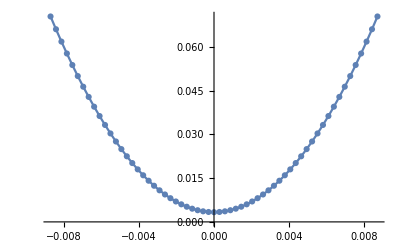

```mathematica
muVals=sol[[All,1,1,2]];
ListPlot[Transpose[{α0,muVals}],Joined->True,PlotMarkers->Automatic]
```

```mathematica
alpha0=N[α0];
Export[{NotebookDirectory[]<>"myfile.csv"},{alpha0,muVals},"CSV"]
```

{C:\Jupyter_Python\EVE-spectrum-correction\mma_proof\myfile.csv}

```mathematica
N[α0]
```

{-0.00872665,-0.00843576,-0.00814487,-0.00785398,-0.00756309,-0.00727221,-0.00698132,-0.00669043,-0.00639954,-0.00610865,-0.00581776,-0.00552688,-0.00523599,-0.0049451,-0.00465421,-0.00436332,-0.00407243,-0.00378155,-0.00349066,-0.00319977,-0.00290888,-0.00261799,-0.00232711,-0.00203622,-0.00174533,-0.00145444,-0.00116355,-0.000872665,-0.000581776,-0.000290888,0.,0.000290888,0.000581776,0.000872665,0.00116355,0.00145444,0.00174533,0.00203622,0.00232711,0.00261799,0.00290888,0.00319977,0.00349066,0.00378155,0.00407243,0.00436332,0.00465421,0.0049451,0.00523599,0.00552688,0.00581776,0.00610865,0.00639954,0.00669043,0.00698132,0.00727221,0.00756309,0.00785398,0.00814487,0.00843576,0.00872665}

```mathematica
ClearAll[eq1,eq2];
eq1[μs_,σs_]:=A*μs^3-B*μs^2+(σ^2-α0^2)*μs-ro^2;
eq2[μs_,σs_]:=-A*μs^2+2*B*μs+(σ^2-α0^2);

(*Define parameters*)
A=915.52;
B=0.9246;
ro=0.00465;
σ=0.04247;

(*Solve the equations for different values of α0*)
results={};
Block[{α0},Do[α0=i*Pi/360;
sol=NSolve[{eq1[μs,σs]==0,eq2[μs,σs]==0,σs>0,μs>0},{μs,σs},Reals];
AppendTo[results,{i,sol}],{i,-30,30}]]

(*Print the results*)
TableForm[Flatten[results,1],TableHeadings->{None,{"α0","μs","σs"}}]
```